```mathematica
Clear["Global`*"];
rep={Ωc->10 (*MHz*),Δp->0,Δs->0,Γs->645 10^-6(*MHz*),Γr->3457 10^-6(*MHz*),Γe->35.9(*MHz*)};

k1=Tuples[{0,1},3];
scaleList=Table[{i},{i,0.05,3, 0.5}];
Lengthscale=Length[scaleList];
resultsList={};
(*For[scale=1, scale<Lengthscale+1, scale++,{*)
(*scale=1;*)
(*For[folderid=1, folderid<9, folderid++,{*)
(*folderid=3;*)
Table[{
k=k1⟦folderid⟧;
path=StringJoin[{ParentDirectory[ParentDirectory[NotebookDirectory[]]],StringReplace["\\data\\20_bins\\20bins\\γ",{"γ"->StringJoin[{ToString[k⟦1⟧],ToString[k⟦2⟧],ToString[k[[3]]]}]}]}];
SetDirectory[path];
resultList=Table[{},{i,20}];
Table[{

data1=Import[StringJoin[path, ToString[StringForm["\\``",FileNames[]⟦id⟧ ]]],"TSV"];
DATA1=Table[data1[[i,j]],{i,2,Length[data1]},{j,{1,3}}];DATA1⟦All,2⟧=(DATA1⟦All,2⟧-Min[DATA1⟦All,2⟧])/(Max[DATA1⟦All,2⟧]-Min[DATA1⟦All,2⟧]);
Data1=Table[0,{i,1,Length[DATA1]},{j,1,2}];
(*time=TimeUsed[];*)
For[i=1,i<Length[DATA1]+1,i++,
{Data1[[i,1]]=(DATA1[[i,1]])*1000,
Data1[[i,2]]=DATA1[[i,2]]}];

Ec=A1 Cos[w1*t+α20]+A2 Cos[w2*t+α19]+A3 Cos[w3*t+α18]+A4 Cos[w4*t+α17]+A5 Cos[w5*t+α16]+A6 Cos[w6*t+α15]+A7 Cos[w7*t+α14]+A8 Cos[w8*t+α13]+A9 Cos[w9*t+α12]+A10 Cos[w10*t+α11]+A11 Cos[w11*t+α10]+A12 Cos[w12*t+α9]+A13 Cos[w13*t+α8]+A14 Cos[w14*t+α7]+A15 Cos[w15*t+α6]+A16 Cos[w16*t+α5]+A17 Cos[w17*t+α4]+A18 Cos[w18*t+α3]+A19 Cos[w19*t+α2]+A20 Cos[w20*t+α1];
Es=-(A1 Sin[w1*t+α20]+A2 Sin[w2*t+α19]+A3 Sin[w3*t+α18]+A4 Sin[w4*t+α17]+A5 Sin[w5*t+α16]+A6 Sin[w6*t+α15]+A7 Sin[w7*t+α14]+A8 Sin[w8*t+α13]+A9 Sin[w9*t+α12]+A10 Sin[w10*t+α11]+A11 Sin[w11*t+α10]+A12 Sin[w12*t+α9]+A13 Sin[w13*t+α8]+A14 Sin[w14*t+α7]+A15 Sin[w15*t+α6]+A16 Sin[w16*t+α5]+A17 Sin[w17*t+α4]+A18 Sin[w18*t+α3]+A19 Sin[w19*t+α2]+A20 Sin[w20*t+α1]);
A1=A2=A3=A4=A5=A6=A7=A8=A9=A10=A11=A12=A13=A14=A15=A16=A17=A18=A19=1;A20=10;
w1=1*12.56;w2=2*12.56;w3=3*12.56;w4=4*12.56;w5=5*12.56;w6=6*12.56;w7=7*12.56;w8=8*12.56;w9=9*12.56;w10=10*12.56;w11=11*12.56;w12=12*12.56;
w13=13*12.56;w14=14*12.56;w15=15*12.56;w16=16*12.56;w17=17*12.56;w18=18*12.56;w19=19*12.56;w20=20*12.56;
Ωs=Ae √(Ec^2+Es^2);

α1=0;

ρeg[Γr_,t_,Γs_,Γe_,Ωc_,Δc_]:=(Γs (-Γs/2-ⅈ (Δc+Δp+Δs)) Ωc ((ⅈ (Γr+2 ⅈ Δc+2 ⅈ Δp))/Ωc+(ⅈ Ωs^2)/((Γs+2 ⅈ Δc+2 ⅈ Δp+2 ⅈ Δs) Ωc)))/(4 ((-Γs/2-ⅈ (Δc+Δp+Δs)) (Γs (-Γe/2-ⅈ Δp) (-Γr/2-ⅈ (Δc+Δp))+(Γs Ωc^2)/4)+1/4 Γs (-Γe/2-ⅈ Δp) Ωs^2));

TT[A_,B_,Γr_,t_,Ae_,α2_,α3_,α4_,α5_,α6_,α7_,α8_,α9_,α10_,α11_,α12_,α13_,α14_,α15_,α16_,α17_,α18_,α19_,α20_,Γs_,Γe_,Ωc_,Δc_]=A(Exp[Im[-ρeg[Γr ,t,Γs,Γe,Ωc,Δc]]]-B);

aa=FindFit[Data1,{TT[A,B,Γr,t,Ae,α2,α3,α4,α5,α6,α7,α8,α9,α10,α11,α12,α13,α14,α15,α16,α17,α18,α19,α20,Γs,Γe,Ωc,Δc]/.rep,-Pi<=α2<=0,-Pi<=α3<=0,-Pi<=α4<=0,-Pi<=α5<=0,-Pi<=α6<=0,-Pi<=α7<=0,-Pi<=α8<=0,-Pi<=α9<=0,-Pi<=α10<=0,-Pi<=α11<=0,-Pi<=α12<=0,-Pi<=α13<=0,-Pi<=α14<=0,-Pi<=α15<=0,-Pi<=α16<=0,-Pi<=α17<=0,-Pi<=α18<=0,-Pi<=α19<=0,-Pi<=α20<=0,-0.01≤t0≤0.01,Ae>0},{α2,α3,α4,α5,α6,α7,α8,α9,α10,α11,α12,α13,α14,α15,α16,α17,α18,α19,α20,Δc,{A,25},B,{t0,0},Ae},t];
(*,{t0,0.002329724271881159}*)
bb=Table[{t,TT[A,B,Γr,t,Ae,α2,α3,α4,α5,α6,α7,α8,α9,α10,α11,α12,α13,α14,α15,α16,α17,α18,α19,α20,Γs,Γe,Ωc,Δc]/.aa/.rep},{t,0,1,0.0002}];

(*TimeList[[id]]=TimeUsed[]-time;*)
results={-Round[(α20/.aa)/Pi]*262144-Round[(α19/.aa)/Pi]*131072-Round[(α18/.aa)/Pi]*65536-Round[(α17/.aa)/Pi]*32768-Round[(α16/.aa)/Pi]*16384-Round[(α15/.aa)/Pi]*8192-Round[(α14/.aa)/Pi]*4096-Round[(α13/.aa)/Pi]*2048-Round[(α12/.aa)/Pi]*1024-Round[(α11/.aa)/Pi]*512-Round[(α10/.aa)/Pi]*256-Round[(α9/.aa)/Pi]*128-Round[(α8/.aa)/Pi]*64-Round[(α7/.aa)/Pi]*32-Round[(α6/.aa)/Pi]*16-Round[(α5/.aa)/Pi]*8-Round[(α4/.aa)/Pi]*4-Round[(α3/.aa)/Pi]*2-Round[(α2/.aa)/Pi]};
results1=StringJoin[ToString@{-Round[(α20/.aa)/Pi],-Round[(α19/.aa)/Pi],-Round[(α18/.aa)/Pi],-Round[(α17/.aa)/Pi],-Round[(α16/.aa)/Pi],-Round[(α15/.aa)/Pi],-Round[(α14/.aa)/Pi],-Round[(α13/.aa)/Pi],-Round[(α12/.aa)/Pi],-Round[(α11/.aa)/Pi],-Round[(α10/.aa)/Pi],-Round[(α9/.aa)/Pi],-Round[(α8/.aa)/Pi],-Round[(α7/.aa)/Pi],-Round[(α6/.aa)/Pi],-Round[(α5/.aa)/Pi],-Round[(α4/.aa)/Pi],-Round[(α3/.aa)/Pi],-Round[(α2/.aa)/Pi]}];
resultList⟦id⟧=-Round[(α20/.aa)/Pi]*4-Round[(α19/.aa)/Pi]*2-Round[(α18/.aa)/Pi];
(*}];*)

(*Print[results[[id]]];*)
(*ListPlot[{Data1,bb},FrameLabel->{" Time (ms)","Transmission (a.u.)"},PlotRange->All,FrameStyle->Directive[14],LabelStyle->{16,GrayLevel[0]},Joined->{False,True},Frame->True,PlotStyle->{{Black,PointSize[0.008]},{Red,Thickness[0.0055]}},AspectRatio->0.5,PlotLabel->StringForm["Tru=``, pred=``",folderid-1,results1]]*)
},{id,1,20}];
Print[resultList]
},{folderid,1,8}]
```

{0,0,0,0,0,0,0,6,0,0,0,0,0,0,7,0,0,0,0,0}

{0,0,0,1,4,4,4,0,0,0,0,1,4,0,0,0,0,0,0,7}

{0,0,6,2,2,0,2,0,2,0,2,1,0,2,2,2,0,2,0,2}

{0,0,0,0,1,0,0,5,2,0,0,0,0,0,0,0,0,0,0,0}

{1,6,6,0,6,1,1,1,0,1,1,6,1,0,0,0,6,0,5,0}

{0,0,0,0,5,5,2,0,0,0,0,0,2,0,0,2,2,2,0,2}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{3,0,3,3,0,3,3,4,1,4,3,0,2,3,4,0,0,0,3,3}

{0,0,0,0,7,0,0,0,3,0,5,0,0,0,0,0,0,0,1,0}

{{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null}}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

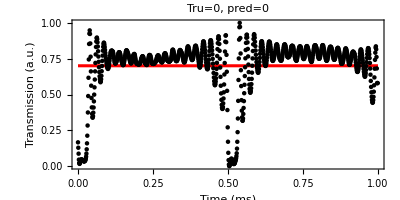
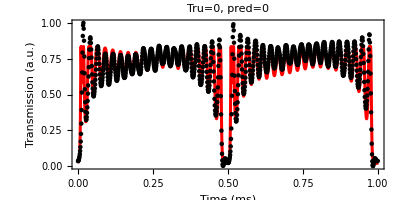
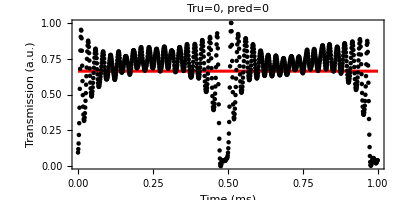
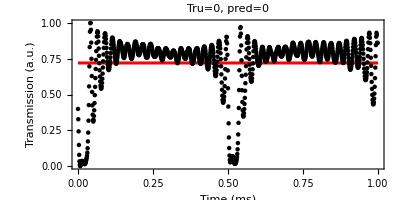
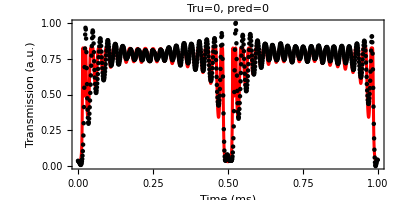
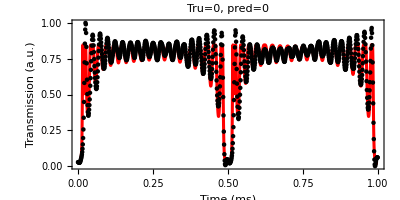
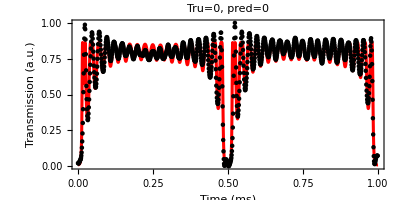
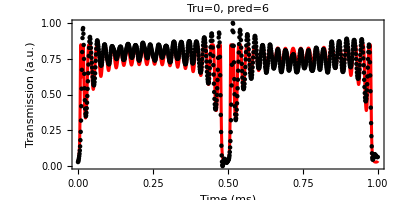
{{{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}},{{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}},{{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}},{{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}},{{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}},{{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}},{{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}},{{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}}}

```mathematica
Clear["Global`*"];
rep={Ωc->10,Δp->0,Δs->0,Γs->645 10^-6,Γr->3457 10^-6,Γe->35.9};

k1=Tuples[{0,1},3];
(*For[scale=1, scale<Lengthscale+1, scale++,{*)
(*scale=1;*)
(*For[folderid=1, folderid<9, folderid++,{*)
(*folderid=3;*)
Table[{
k=k1⟦folderid⟧;
path=StringJoin[{ParentDirectory[ParentDirectory[NotebookDirectory[]]],StringReplace["\\data\\20_bins\\20bins\\γ",{"γ"->StringJoin[{ToString[k⟦1⟧],ToString[k⟦2⟧],ToString[k[[3]]]}]}]}];

SetDirectory[path];
Table[{

data1=Import[StringJoin[path, ToString[StringForm["\\``",FileNames[]⟦id⟧ ]]],"TSV"];
DATA1=Table[data1[[i,j]],{i,2,Length[data1]},{j,{1,3}}];DATA1⟦All,2⟧=(DATA1⟦All,2⟧-Min[DATA1⟦All,2⟧])/(Max[DATA1⟦All,2⟧]-Min[DATA1⟦All,2⟧]);
Data1=Table[0,{i,1,Length[DATA1]},{j,1,2}];
(*time=TimeUsed[];*)
For[i=1,i<Length[DATA1]+1,i++,
{Data1[[i,1]]=(DATA1[[i,1]])*1000,
Data1[[i,2]]=DATA1[[i,2]]}];

Ec=A1 Cos[w1*t+α20]+A2 Cos[w2*t+α19]+A3 Cos[w3*t+α18]+A4 Cos[w4*t+α17]+A5 Cos[w5*t+α16]+A6 Cos[w6*t+α15]+A7 Cos[w7*t+α14]+A8 Cos[w8*t+α13]+A9 Cos[w9*t+α12]+A10 Cos[w10*t+α11]+A11 Cos[w11*t+α10]+A12 Cos[w12*t+α9]+A13 Cos[w13*t+α8]+A14 Cos[w14*t+α7]+A15 Cos[w15*t+α6]+A16 Cos[w16*t+α5]+A17 Cos[w17*t+α4]+A18 Cos[w18*t+α3]+A19 Cos[w19*t+α2]+A20 Cos[w20*t+α1];
Es=-(A1 Sin[w1*t+α20]+A2 Sin[w2*t+α19]+A3 Sin[w3*t+α18]+A4 Sin[w4*t+α17]+A5 Sin[w5*t+α16]+A6 Sin[w6*t+α15]+A7 Sin[w7*t+α14]+A8 Sin[w8*t+α13]+A9 Sin[w9*t+α12]+A10 Sin[w10*t+α11]+A11 Sin[w11*t+α10]+A12 Sin[w12*t+α9]+A13 Sin[w13*t+α8]+A14 Sin[w14*t+α7]+A15 Sin[w15*t+α6]+A16 Sin[w16*t+α5]+A17 Sin[w17*t+α4]+A18 Sin[w18*t+α3]+A19 Sin[w19*t+α2]+A20 Sin[w20*t+α1]);
A1=A2=A3=A4=A5=A6=A7=A8=A9=A10=A11=A12=A13=A14=A15=A16=A17=A18=A19=1;A20=10;
w1=1*12.56;w2=2*12.56;w3=3*12.56;w4=4*12.56;w5=5*12.56;w6=6*12.56;w7=7*12.56;w8=8*12.56;w9=9*12.56;w10=10*12.56;w11=11*12.56;w12=12*12.56;
w13=13*12.56;w14=14*12.56;w15=15*12.56;w16=16*12.56;w17=17*12.56;w18=18*12.56;w19=19*12.56;w20=20*12.56;
Ωs=Ae √(Ec^2+Es^2);

α1=0;

ρeg[Γr_,t_,Γs_,Γe_,Ωc_,Δc_]:=(Γs (-Γs/2-ⅈ (Δc+Δp+Δs)) Ωc ((ⅈ (Γr+2 ⅈ Δc+2 ⅈ Δp))/Ωc+(ⅈ Ωs^2)/((Γs+2 ⅈ Δc+2 ⅈ Δp+2 ⅈ Δs) Ωc)))/(4 ((-Γs/2-ⅈ (Δc+Δp+Δs)) (Γs (-Γe/2-ⅈ Δp) (-Γr/2-ⅈ (Δc+Δp))+(Γs Ωc^2)/4)+1/4 Γs (-Γe/2-ⅈ Δp) Ωs^2));

TT[A_,B_,Γr_,t_,Ae_,α2_,α3_,α4_,α5_,α6_,α7_,α8_,α9_,α10_,α11_,α12_,α13_,α14_,α15_,α16_,α17_,α18_,α19_,α20_,Γs_,Γe_,Ωc_,Δc_]=A(Exp[Im[-ρeg[Γr ,t,Γs,Γe,Ωc,Δc]]]-B);

aa=FindFit[Data1,{TT[A,B,Γr,t,Ae,α2,α3,α4,α5,α6,α7,α8,α9,α10,α11,α12,α13,α14,α15,α16,α17,α18,α19,α20,Γs,Γe,Ωc,Δc]/.rep,-Pi<=α2<=0,-Pi<=α3<=0,-Pi<=α4<=0,-Pi<=α5<=0,-Pi<=α6<=0,-Pi<=α7<=0,-Pi<=α8<=0,-Pi<=α9<=0,-Pi<=α10<=0,-Pi<=α11<=0,-Pi<=α12<=0,-Pi<=α13<=0,-Pi<=α14<=0,-Pi<=α15<=0,-Pi<=α16<=0,-Pi<=α17<=0,-Pi<=α18<=0,-Pi<=α19<=0,-Pi<=α20<=0,-0.01≤t0≤0.01,Ae>0},{α2,α3,α4,α5,α6,α7,α8,α9,α10,α11,α12,α13,α14,α15,α16,α17,α18,α19,α20,Δc,{A,25},B,{t0,0},Ae},t];
(*,{t0,0.002329724271881159}*)
bb=Table[{t,TT[A,B,Γr,t,Ae,α2,α3,α4,α5,α6,α7,α8,α9,α10,α11,α12,α13,α14,α15,α16,α17,α18,α19,α20,Γs,Γe,Ωc,Δc]/.aa/.rep},{t,0,1,0.0002}];

(*TimeList[[id]]=TimeUsed[]-time;*)
results={-Round[(α20/.aa)/Pi]*262144-Round[(α19/.aa)/Pi]*131072-Round[(α18/.aa)/Pi]*65536-Round[(α17/.aa)/Pi]*32768-Round[(α16/.aa)/Pi]*16384-Round[(α15/.aa)/Pi]*8192-Round[(α14/.aa)/Pi]*4096-Round[(α13/.aa)/Pi]*2048-Round[(α12/.aa)/Pi]*1024-Round[(α11/.aa)/Pi]*512-Round[(α10/.aa)/Pi]*256-Round[(α9/.aa)/Pi]*128-Round[(α8/.aa)/Pi]*64-Round[(α7/.aa)/Pi]*32-Round[(α6/.aa)/Pi]*16-Round[(α5/.aa)/Pi]*8-Round[(α4/.aa)/Pi]*4-Round[(α3/.aa)/Pi]*2-Round[(α2/.aa)/Pi]};
results1=StringJoin[ToString@{-Round[(α20/.aa)/Pi],-Round[(α19/.aa)/Pi],-Round[(α18/.aa)/Pi],-Round[(α17/.aa)/Pi],-Round[(α16/.aa)/Pi],-Round[(α15/.aa)/Pi],-Round[(α14/.aa)/Pi],-Round[(α13/.aa)/Pi],-Round[(α12/.aa)/Pi],-Round[(α11/.aa)/Pi],-Round[(α10/.aa)/Pi],-Round[(α9/.aa)/Pi],-Round[(α8/.aa)/Pi],-Round[(α7/.aa)/Pi],-Round[(α6/.aa)/Pi],-Round[(α5/.aa)/Pi],-Round[(α4/.aa)/Pi],-Round[(α3/.aa)/Pi],-Round[(α2/.aa)/Pi]}];
result2=-Round[(α20/.aa)/Pi]*4-Round[(α19/.aa)/Pi]*2-Round[(α18/.aa)/Pi];
(*}];*)

(*Print[results[[id]]];*)
ListPlot[{Data1,bb},FrameLabel->{" Time (ms)","Transmission (a.u.)"},PlotRange->All,FrameStyle->Directive[14],LabelStyle->{16,GrayLevel[0]},Joined->{False,True},Frame->True,PlotStyle->{{Black,PointSize[0.008]},{Red,Thickness[0.0055]}},AspectRatio->0.5,PlotLabel->StringForm["Tru=``, pred=``",folderid-1,result2]]
},{id,1,20}]
(*Print[resultList]*)
},{folderid,1,8}]
```